# 23 Cholesky Decomposition

It is not uncommon for matrices to be symmetric A=Aᵀ  and positive definite i.e.
	x.A.x>0 for x≠0
Amongst other things this means that A has only positive real eigenvalues!  It also means you can compute a symmetric LU decomposition 
	A=Rᵀ.R	
with R upper triangular without pivoting.  There is an entirely equivalent version with lower triangular L.

Officially this Cholesky decomposition takes half the flops of an LU decomposition.  Practically the fact that you do not need to pivot means it frequently takes less than half the time.

```mathematica
m=1234;
A=RandomReal[{-1,1},{m,m}]; A= Aᵀ.A;
AbsoluteTiming[R=CholeskyDecomposition[A];]
AbsoluteTiming[LUDecomposition[A];]
MatrixPlot[R,PlotLabel->Norm[A-Rᵀ.R]]
```

{0.0220618,Null}

{0.0521497,Null}

-Graphics-

The question is how to work out and arrange the algorithm.

## Start Small: m=2

Suppose I have a positive symmetric positive definite 2×2 matrix
	(a11 | a12
a12 | a22)
Note a11>0.  Our target is to write this matrix as 
	(a11 | a12
a12 | a22)=(b1 | 0
b2 | b3).(b1 | 0
b2 | b3)^ᵀ=(b1 | 0
b2 | b3).(b1 | b2
0 | b3)=(b1^2 | b1*b2
b1*b2 | b2^2+b3^2)
This works if 
	a11  | = | b1^2 
a12 | = | b1 b2
a22 | = | b2^2+b3^2
Solving this we get 
	b1 | = | √a11
b2 | = | a12/b1
b3 | = | √(a22-b2^2)
Here is a baby function

```mathematica
Chol2[A_]:= Module[{b1,b2,b3},
b1=√A⟦1,1⟧;
b2=A⟦1,2⟧/b1;
b3=√(A⟦2,2⟧-b2^2);
({{b1, b2}, {0, b3}})
]
```

As always test!

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A =A.Aᵀ;
R=Chol2[A];
Norm[A-Rᵀ.R]
```

6.93889×10^-18

## Try Bigger: m=3

Suppose I have a positive symmetric positive definite 2×2 matrix
	(a11 | a12 | a13
a12 | a22 | a23
a13 | a23 | a33)
Note a11>0.  Our target is to write this matrix as 
	(a11 | a12 | a13
a12 | a22 | a23
a13 | a23 | a33)=(b1 | 0 | 0
b2 | b3 | 0
b4 | b5 | b6).(b1 | 0 | 0
b2 | b3 | 0
b4 | b5 | b6)^ᵀ=(b1^2 | b1 b2 | b1 b4
b1 b2 | b2^2+b3^2 | b2 b4+b3 b5
b1 b4 | b2 b4+b3 b5 | b4^2+b5^2+b6^2)
The top row and the left most columns work if 
	a11  | = | b1^2 
a12 | = | b1 b2
a13 | = | b1b4
Note we are going to worry about the rest latter. Solving this we get 
	b1 | = | √a11
(b2
b4) | = | (a12
a13)/b1
We can go down a dimension (on the top and the side) which will leave us with a 2×2 that we already worked out how to do. The way to organize this incremental approach is as follows
	(a11 | wᵀ
w | K)=(α | 0
w/α | I).(1 | 0
0 | K̂).(α | wᵀ/α
0 | I)=(α^2 | wᵀ
w | K̂+1/α^2 w.wᵀ)
where if you expand stuff out (along the row and down the column) we need
	α^2 | = | a11
K̂+1/α^2 w.wᵀ | = | K
Solving for the stuff we do not know we get
	α | = | √a11 |   |  
K̂ | = | K-1/α^2 w.wᵀ | = | K-1/a11 w⊗w
Note this recipe works for a general m.

## General m: Single Step Code

```mathematica
CholStep[A_]:= Module[{m=Length[A],α,w,K,KNew,R=IdentityMatrix[m];},
α=√A⟦1,1⟧;
w=A⟦2;;m,1⟧;
KNew=A⟦2;;m,2;;m⟧-KroneckerProduct[w,w]/A⟦1,1⟧;
R⟦1,1⟧=α;
R⟦2;;m,1⟧=w;
]
```

Suppose I have a block decomposition of a positive symmetric positive definite m×m matrix
	(a11 | wᵀ
w | K)
where a11 is a scalar, K is a (m-1)×(m-1) symmetric block matrix and w is a column vector!
Note a11>0.  Our target is to write this matrix as 
	(a11 | wᵀ
w | K)=(α | 0
w/α | I).(1 | 0
0 | b3).(α | 0
w/α | I)^ᵀ=(b1^2 | b1 b2
b1 b2 | b2^2+b3^2)
The top row and the left most columns work if 
	a11  | = | b1^2 
a12 | = | b1 b2
a13 | = | b1b4
Note we are going to worry about the rest latter. Solving this we get 
	b1 | = | √a11
(b2
b4) | = | (a12
a13)/b1
We can go down a dimension (on the top and the side) which will leave us with a 2×2 that we already worked out how to do.

## Break

Here is our Pivoted LU Code

```mathematica
Clear[b1,b2,b3,b4,b5,b6]
L={{b1,0,0},{b2,b3,0},{b4,b5,b6}};
MatrixForm[L.Lᵀ]
```

(b1^2 | b1 b2 | b1 b4
b1 b2 | b2^2+b3^2 | b2 b4+b3 b5
b1 b4 | b2 b4+b3 b5 | b4^2+b5^2+b6^2)

```mathematica
({{b1^2, b1 b2, b1 b4}, {b1 b2, {{b2^2+b3^2, b2 b4+b3 b5}, {b2 b4+b3 b5, b4^2+b5^2+b6^2}}, □}, {b1 b4, □, □}})
```

```mathematica
({{b1, 0}, {b2, b3}}).({{b1, b2}, {0, b3}})
```

Dot::rect: Nonrectangular tensor encountered.

{{{-0.535384,0.99848,-0.00271323,-0.696879,0.26555,9991,0.835621,-0.925548,0.913357,0.408536},0},{1}}.{1}
 |  |  |  |

```mathematica
Clear[LUTogetherPivoted]
LUTogetherPivoted[A_]:=Module[{m=Length[A],LU=A, p, col ,i},
p=Range[m]; 
Do[
(* Find Max Position *)
col=Abs[LU⟦All,k⟧]; col⟦1;;k-1⟧*=0;
i=FirstPosition[col,Max[col]]⟦1⟧;
(* Switch Rows Book Keeping *)
p⟦{k,i}⟧=p⟦{i,k}⟧;
(* Switch Rows *)
LU⟦{k,i}⟧=LU⟦{i,k}⟧;
Do[
LU⟦j,k⟧=LU⟦j,k⟧/LU⟦k,k⟧;
(* Diagonals store U not L. Index range excludes the diagonal. *)
LU⟦j,k+1;;m⟧-=LU⟦j,k⟧ LU⟦k,k+1;;m⟧,
{j,k+1,m}],
{k,1,m-1}];
(* Splitting LU to maintain the return values *)
{LowerTriangularize[LU,-1]+IdentityMatrix[m],UpperTriangularize[LU],p}
]
```

As always test!

```mathematica
m=123;A=RandomReal[{-1,1},{m,m}];
{L,U,p}=LUTogetherPivoted[A];
Norm[A⟦p⟧-L.U]
TabView[{
"L"->MatrixPlot[L,PlotLegends->Automatic],
"U"->MatrixPlot[U,PlotLegends->Automatic]}];
```

1.71573×10^-14

Pivoting has made sure |L_(i,j)|≤1 for all i and j. On the other hand the U values can (and do) get larger. A common measure of how bad a matrix is for partial pivoting is how big the U entries get!

### Growth Factor

The growth factor for a matrix A=L.U were the LU decomposition is defined by 
	ρ=(max_(i,j) |U_ij|)/(max_(i,j) |A_(i,j)|)
It looks like for random matrices ρ is usually not that big

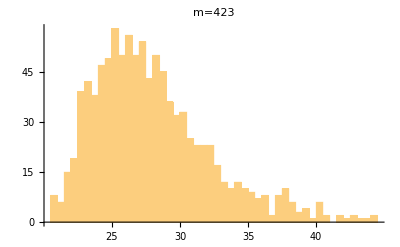

```mathematica
SampleSize=10^3;
m=423;
GrowthFactors=Table[A=RandomReal[{-1,1},{m,m}];
{LU,p,c}=LUDecomposition[A];
Max[LU]/Max[A],{SampleSize}];
Histogram[GrowthFactors,40,
PlotLabel->StringForm["m=``",m]]
```

## Worst Case Growth Factor

Row pivoting works for almost all randomly generated matrices and is very widely used in practice. To see that bad behavior is possible lets try to row reduce the following artificial example.

```mathematica
m=6;
BadMat= LowerTriangularize[ConstantArray[-1,{m,m}],-1]+IdentityMatrix[m];
BadMat⟦All,m⟧=ConstantArray[1,m];
MatrixForm[BadMat]
```

(1 | 0 | 0 | 0 | 0 | 1
-1 | 1 | 0 | 0 | 0 | 1
-1 | -1 | 1 | 0 | 0 | 1
-1 | -1 | -1 | 1 | 0 | 1
-1 | -1 | -1 | -1 | 1 | 1
-1 | -1 | -1 | -1 | -1 | 1)

```mathematica
Clear[A,m]
m=6;
BadMat= LowerTriangularize[ConstantArray[-1,{m,m}],-1]+IdentityMatrix[m];
BadMat⟦All,m⟧=ConstantArray[1,m];
A[0]=BadMat;
A[k_]:=A[k]=Module[{M=A[k-1]}, 
m= Length[M];Do[M⟦i⟧+=M⟦k⟧,{i,k+1,m}];
M]
TabView[Map[MatrixForm,Map[A,Range[m]-1]]]
```

123456

So row reduction with row pivoting can certainly produce large values! This is in fact the worst possible growth factor of 2^(m-1)! Technically row pivoting makes an LU Decomposition backward stable.  However, the worst possible case constant is 2^(m-1) which is big enough to make that conclusion silly!

## Practical Considerations

In real world matrices growth factors are well behaved and partial pivoting is widely used for dense matrices that fit in computer memory.

### Storing and Using an LU Decomposition

Most of the work in solving a linear system is in the LU decomposition!  It is not uncommon to need to solve several systems with the same right hand side. If you need to do this you should save and recycle the LU Decomposition.

In Mathematica this looks like this with timings attached.

```mathematica
m=10^4;
A=RandomReal[{-1,1},{m,m}];
{b1,b2,b3,b4}=RandomReal[{-1,1},{4,m}];
Timing[ LSolFun=LinearSolve[A];]
Timing[ LSolFun[b1];LSolFun[b2];LSolFun[b3];LSolFun[b4];]
Timing[ LSolFun=LinearSolve[A,b1];]
Timing[ LSolFun=LinearSolve[A,b2];]
Timing[ LSolFun=LinearSolve[A,b3];]
Timing[ LSolFun=LinearSolve[A,b4];]
```

{5.15625,Null}

{0.234375,Null}

{5.35938,Null}

{5.4375,Null}

{5.29688,Null}

{5.42188,Null}